This script is a part of ANGEL project.
V 1.5.2
2017.12.14
(C) Vulpes Corsac

```mathematica
Clear["Global`*"];(* Variables clearing *)
```

```mathematica
Needs["ErrorBarPlots`"];(* Including Package to use ErrorBar plotting *)
```

```mathematica
(* Manual settings *)
λ=1550;(* Wavelength *)
importDir="ImportData";(* Directory for raw data importing *)
exportDir="ExportData";(* Directory for calculated data exporting *)
AllData=Import["dataSample.xlsx", Path->FileNameJoin[{NotebookDirectory[ ],importDir}]];(* Filename with input data *)
UsePowerNoise=True;(* Whether to use power noise (zero power is actually not zero) : True - yes | False - no *)
```

```mathematica
(* DO NOT TOUCH ANYTHING AFTERWARDS - MAIN SCRIPT IS THERE *)
```

```mathematica
PrependTo[AllData,AllData[[1]]];(* Script ignores the first list in Exel file. That is why I copy it and insert it in the first position *)
```

```mathematica
(* IT DOES NOT WORK AS IT SHOULD! *)
Off[CreateDirectory::filex]; (* Turning off warning message about creating already existing directory *)
importDir=FileNameJoin[{NotebookDirectory[ ],importDir}];(* Getting full export directory path *)
exportDir=FileNameJoin[{NotebookDirectory[ ],exportDir}];(* Getting full export directory path *)
If[DirectoryQ[exportDir],,CreateDirectory[exportDir]];(* Creating directory for exporting all calculated data *)
```

```mathematica
Experiments = Length[AllData];(* Getting experiment points ammount as a number ol lists in Exel file *)
BeamERFPlot=Table[{0},{i,1,Experiments}];(* Preparing table for ERF function data plotting *)
BeamERFExport=Table[{0},{i,1,Experiments}];(* Preparing table for ERF function data exporting *)
BeamGaussPlot=Table[{0},{i,1,Experiments}];(* Preparing table for Gauss function data plotting *)
BeamGaussExport=Table[{0},{i,1,Experiments}]; (* Preparing table for Gauss function data exporting *)
BeamERFCenterExport=Table[{0},{i,1,Experiments}]; (* Preparing table for ERF beam center exporting *)
BeamGaussCenterExport=Table[{0},{i,1,Experiments}]; (* Preparing table for Gauss beam center exporting *)
BeamERFCenterPlot=Table[{0},{i,1,Experiments}]; (* Preparing table for ERF beam center plotting *)
BeamGaussCenterPlot=Table[{0},{i,1,Experiments}]; (* Preparing table for Gauss beam center plotting *)
```

```mathematica
PmeasuredErf[P0_,P1_,P2_,P3_,Px_,Sgn_]:=P0+P1/2×(1+Sign[Sgn]×Erf[(√2(Px-P2))/P3]);(* ERF fitting function *)
GaussFunction[y0_,A_,xc_,σ_,x_]:=y0+A Exp[-(x-xc)^2/(2 σ^2)];(* Gauss fitting function *)
BeamPropogationFunction[A2_,A1_,A0_,x_]:=Re[√(A2 x^2+A1 x+A0)];(* Hyperbolic fitting function for beam parameters calculation *)
```

```mathematica
(* Beam parameters calculation via hyperbolic fitting *)
GetBeamPropogationFit[data_List,Mode_]:=(
dataFit=data[[All,1]];(* Getting round data *)
nlm=NonlinearModelFit[dataFit,BeamPropogationFunction[A2,A1,A0,x],{A2,A1,A0},x];(* Fitting *)
parametersTable = nlm["ParameterTable"];(* Getting fitting parameters table, and coefficients and their errors *)
If[NumericQ[ToExpression[nlm["RSquared"]]],R2=ToString[nlm["RSquared"]],R2="UNDEFINED"];
A2fit=parametersTable[[1,1,2,2]];δA2fit=parametersTable[[1,1,2,3]];
A1fit=parametersTable[[1,1,3,2]];δA1fit=parametersTable[[1,1,3,3]];
A0fit=parametersTable[[1,1,4,2]];δA0fit=parametersTable[[1,1,4,3]];
(* Parameters from ГОСТ (ISO) and their errors *)
z0=-A1fit/(2A2fit);δz0=((2A2fit) (-δA1fit)+(-A1fit)(2δA2fit))/(2A2fit)^2;
dσ0=Re[1/(2 √A2fit)√(4A0fit A2fit-A1fit^2)];δdσ0=Re[1/(2 √A2fit)^2((2 √A2fit) ((4(A0fit δA2fit+A2fit δA0fit)+2 A1fit δA1fit)/(2 √(4A0fit A2fit-A1fit^2)))+(√(4A0fit A2fit-A1fit^2))(1/2 δA2fit/(2 A2fit)))];
Θσ=Re[√A2fit];δΘσ=Re[δA2fit/(2 A2fit)];
zR=Re[1/(2A2fit)√(4A0fit A2fit-A1fit^2)];δzR=Re[1/(2A2fit)^2((2A2fit) ((4(A0fit δA2fit+A2fit δA0fit)+2 A1fit δA1fit)/(2 √(4A0fit A2fit-A1fit^2)))+(√(4A0fit A2fit-A1fit^2))(2δA2fit))];
M2=Re[π/(8λ)√(4A0fit A2fit-A1fit^2)];δM2=Re[π/(8λ)(4(A0fit δA2fit+A2fit δA0fit)+2 A1fit δA1fit)/(2 √(4A0fit A2fit-A1fit^2))];
BeamRadiusesFitString="Beam diameters "<>Mode<> " fit ( Sqrt[A2*x^2+A1*x+A0] ) :"<>"\n\t"<> (* Forming string with all parameters for later export *)
"A2 = "<>ToString[A2fit]<>" ± "<>ToString[δA2fit]<>", t.m. "<>ToString[100×Abs[δA2fit/A2fit]]<>" %"<>"\n\t"<>
"A1 = "<>ToString[A1fit]<>" ± "<>ToString[δA1fit]<>", t.m. "<>ToString[100×Abs[δA1fit/A1fit]]<>" %"<>"\n\t"<>
"A0 = "<>ToString[A0fit]<>" ± "<>ToString[δA0fit]<>", t.m. "<>ToString[100×Abs[δA0fit/A0fit]]<>" %"<>"\n"<>
"From ГОСТ Р ИСО 11146-1-2008-1 ( ISO 11146-1:2005 ):"<>"\n\t"<>
"z0[waist coordinate] = "<>ToString[z0]<>" ± "<>ToString[δz0]<>", t.m. "<>ToString[100×Abs[δz0/z0]]<>" %"<>"\n\t"<>
"d_sigma0[waist]= "<>ToString[dσ0]<>" ± "<>ToString[δdσ0]<>", t.m. "<>ToString[100×Abs[δdσ0/dσ0]]<>" %"<>"\n\t"<>
"Theta_sigma[divergence angle] = "<>ToString[Θσ]<>" ± "<>ToString[δΘσ]<>", t.m. "<>ToString[100×Abs[δΘσ/Θσ]]<>" %"<>"\n\t"<>
"z_R[Rayleigh distance] = "<>ToString[zR]<>" ± "<>ToString[δzR]<>", t.m. "<>ToString[100×Abs[δzR/zR]]<>" %"<>"\n\t"<>
"M2[Beam quality] = "<>ToString[M2]<>" ± "<>ToString[δM2]<>", t.m. "<>ToString[100×Abs[δM2/M2]]<>" %";
Export[FileNameJoin[{exportDir,"BeamPropogation"<>Mode<>"Fit.txt"}],BeamRadiusesFitString];(* Exporting string from above *)
BeamRadiusesPlot=Show[(* Plotting data and fit on the same plot *)
ErrorListPlot[data,PlotRange->All,Joined->False,PlotLabel->"Beam diameter dependency fitting with "<>Mode<>", R^2 = "<>R2,AxesLabel->{"Knife z","Beam diameter"},ImageSize->Large],
Plot[BeamPropogationFunction[A2fit,A1fit,A0fit,x],{x,Min[data[[All,1]]],Max[data[[All,1]]]},ColorFunction->Function[{x,y},Red],ImageSize->Large]
];
Export[FileNameJoin[{exportDir,"BeamPropogation"<>Mode<>"Plot.png"}],BeamRadiusesPlot];(* Exporting plot from above *)
Return[BeamRadiusesPlot]
);
```

```mathematica
(* Calculating first derivative as it is in Origin *)
MyDerivative[x_List]:=(d=List[];len=Length[x];For[ i = 1,i ≤ len,i++,Which[(* For all points *)
i==1,AppendTo[d, {x[[i,1]],Abs[(x[[i+1,2]]-x[[i,2]])/(x[[i+1,1]]-x[[i,1]])]}],(* First point *)
i>1 && i<len,AppendTo[d, {x[[i,1]],Abs[1/2((x[[i+1,2]]-x[[i,2]])/(x[[i+1,1]]-x[[i,1]])+(x[[i,2]]-x[[i-1,2]])/(x[[i,1]]-x[[i-1,1]]))]}],(* First derivative calculating *)
i==len,AppendTo[d,{x[[i,1]],Abs[(x[[i,2]]-x[[i-1,2]])/(x[[i,1]]-x[[i-1,1]])]}](* Last point *)
]];
Return[d]
);
```

```mathematica
(* Calculating beam profile fitting with ERF *)
CalculateERF[]:=(Monitor[
For[ExperimentRound=1,ExperimentRound<Experiments,ExperimentRound+=1;(* For all experiments (all lists in Exel file) *)
zStep=AllData[[ExperimentRound,1,1]];(* Z coordinate for current experiment *)
Data=AllData[[ExperimentRound,3;;,1;;2]];(* Round data *)
Sgn=Sign[Data[[-1,2]]-Data[[1,2]]];(* Sign in ERF formula *)
If[UsePowerNoise,PowerNoise=Min[Data[[All,2]]],PowerNoise=0];(* If we need power noize fitting, it is Min from all Data, otherwise - 0 *)
BeamPower=Max[Data[[All,2]]]-PowerNoise;(* All beam power is Max minus power noize *)
BeamRadius=(Max[Data[[All,1]]]-Min[Data[[All,1]]])/2;(* Beam radius must be less then half of data range *)
If[UsePowerNoise,(* If there is power noize *)
nlm=NonlinearModelFit[Data,PmeasuredErf[P0,P1,P2,P3,Px,Sgn],
{{P0,PowerNoise},{P1,BeamPower},{P2,(Min[Data[[All,1]]]+Max[Data[[All,1]]])/2},{P3,BeamRadius}},Px],(* Fitting with noize *)
nlm=NonlinearModelFit[Data,PmeasuredErf[PowerNoise,P1,P2,P3,Px,Sgn],
{{P1,BeamPower},{P2,(Min[Data[[All,1]]]+Max[Data[[All,1]]])/2},{P3,BeamRadius}},Px](* Fitting without noize *)
];
parametersTable = nlm["ParameterTable"];(* Getting fitted parameters *)
If[NumericQ[ToExpression[nlm["RSquared"]]],R2=ToString[nlm["RSquared"]],R2="UNDEFINED"];
If[Length[parametersTable[[1,1]]]==5,(* If with noize - there are less parameters *)
P0fit=parametersTable[[1,1,2,2]];δP0fit=parametersTable[[1,1,2,3]];
P1fit=parametersTable[[1,1,3,2]];δP1fit=parametersTable[[1,1,3,3]];
P2fit=parametersTable[[1,1,4,2]];δP2fit=parametersTable[[1,1,4,3]];
P3fit=parametersTable[[1,1,5,2]];δP3fit=parametersTable[[1,1,5,3]];
,
P0fit=0;δP0fit=0;
P1fit=parametersTable[[1,1,2,2]];δP1fit=parametersTable[[1,1,2,3]];
P2fit=parametersTable[[1,1,3,2]];δP2fit=parametersTable[[1,1,3,3]];
P3fit=parametersTable[[1,1,4,2]];δP3fit=parametersTable[[1,1,4,3]];
];
FitDataPlot = Show[(* Plotting data and fit on the same plot *)
ListPlot[Data,PlotRange->All,Joined->False,PlotLabel->"Experiment data ERF fitting, R^2 = "<>R2,AxesLabel->{"Knife x","Power"},ImageSize->Large],
Plot[PmeasuredErf[P0fit,P1fit,P2fit,P3fit,Px,Sgn],{Px,Min[Data[[All,1]]],Max[Data[[All,1]]]},ColorFunction->Function[{x,y},Red],ImageSize->Large]
];
Export[FileNameJoin[{exportDir,"z="<>ToString[zStep]<>"_"<>"ERFFitPlot.png"}],FitDataPlot];(* Exporting plot from above *)
DataFitString="Data fit ( P0 + P1/2 * (1 ± Erf[Sqrt[2](Px-P2)/P3]) ) :"<>"\n\t"<>(* Forming string with all parameters for later export *)
"P0[Power Noise] = "<>ToString[P0fit]<>" ± "<>ToString[Abs[δP0fit]]<>", t.m. "<>ToString[100×Abs[δP0fit/Max[10^-7,P0fit]]]<>" %"<>"\n\t"<>
"P1[Power] = "<>ToString[P1fit]<>" ± "<>ToString[Abs[δP1fit]]<>", t.m. "<>ToString[100×Abs[δP1fit/P1fit]]<>" %"<>"\n\t"<>
"P2[Beam Center] = "<>ToString[P2fit]<>" ± "<>ToString[Abs[δP2fit]]<>", t.m. "<>ToString[100×Abs[δP2fit/P2fit]]<>" %"<>"\n\t"<>
"P3[Beam Radius E-2] = "<>ToString[P3fit]<>" ± "<>ToString[Abs[δP3fit]]<>", t.m. "<>ToString[100×Abs[δP3fit/P3fit]]<>" %";
Export[FileNameJoin[{exportDir,"z="<>ToString[zStep]<>"_"<>"ERFFit.txt"}],DataFitString];(* Exporting string from above *)
BeamERFPlot[[ExperimentRound]]={{zStep, 2 P3fit},ErrorBar[2 δP3fit]};(* Forming data for plotting *)
BeamERFExport[[ExperimentRound]]={zStep, 2 P3fit,2 δP3fit};(* Forming data for exporting *)
BeamERFCenterPlot[[ExperimentRound]]={{zStep, P2fit},ErrorBar[δP2fit]};(* Forming data for plotting *)
BeamERFCenterExport[[ExperimentRound]]={zStep, P2fit,δP2fit};(* Forming data for exporting *)
],{ExperimentRound,zStep}];(* Monitoring current round *)
BeamERFPlot=BeamERFPlot[[2;;]];(* Cutting first fake data *)
BeamERFExport[[1]]={"R","W","dW"};(* Adding column names *)
Export[FileNameJoin[{exportDir,"BeamERF.xlsx"}],BeamERFExport];(* Exporting data from above *)
BeamERFCenterPlot=BeamERFCenterPlot[[2;;]];(* Cutting first fake data *)
BeamERFCenterExport[[1]]={"R","Xc","dXc"};(* Adding column names *)
Export[FileNameJoin[{exportDir,"BeamERFCenter.xlsx"}],BeamERFCenterExport];(* Exporting data from above *)
);
```

```mathematica
(* Calculating beam profile fitting with Gauss *)
CalculateGauss[]:=(Monitor[
For[ExperimentRound=1,ExperimentRound<Experiments,ExperimentRound+=1;(* For all experiments (all lists in Exel file) *)
zStep=AllData[[ExperimentRound,1,1]];(* Z coordinate for current experiment *)
Data=MyDerivative[AllData[[ExperimentRound,3;;,1;;2]]];(* Getting round data *)
If[UsePowerNoise,PowerNoise=Min[Data[[All,2]]],PowerNoise=0];(* If we need power noize fitting, it is Min from all Data, otherwise - 0 *)
BeamPower=Max[Data[[All,2]]]-PowerNoise;(* All beam power is Max minus power noize *)
BeamRadius=(Max[Data[[All,1]]]-Min[Data[[All,1]]])/2;(* Beam radius must be less then half of data range *)
nlm=NonlinearModelFit[Data,GaussFunction[y0,A,xc,σ,x],
{{y0,PowerNoise},{A,BeamPower},{xc,(Min[Data[[All,1]]]+Max[Data[[All,1]]])/2},{σ,BeamRadius/3}},x];(* Fitting with noize *)
parametersTable = nlm["ParameterTable"];(* Getting fitted parameters *)
If[NumericQ[ToExpression[nlm["RSquared"]]],R2=ToString[nlm["RSquared"]],R2="UNDEFINED"];
y0Fit=parametersTable[[1,1,2,2]];δy0Fit=parametersTable[[1,1,2,3]];
AFit=parametersTable[[1,1,3,2]];δAFit=parametersTable[[1,1,3,3]];
xcFit=parametersTable[[1,1,4,2]];δxcFit=parametersTable[[1,1,4,3]];
σFit=Abs[parametersTable[[1,1,5,2]]];δσFit=parametersTable[[1,1,5,3]];
FitDataPlot = Show[(* Plotting data and fit on the same plot *)
ListPlot[Data,PlotRange->All,Joined->False,PlotLabel->"First devariative fitting with Gauss fitting, R^2 = "<>R2,AxesLabel->{"Knife x","Power"},ImageSize->Large],
Plot[GaussFunction[y0Fit,AFit,xcFit,σFit,x],{x,Min[Data[[All,1]]],Max[Data[[All,1]]]},ColorFunction->Function[{x,y},Red],PlotRange->All,ImageSize->Large]
];
Export[FileNameJoin[{exportDir,"z="<>ToString[zStep]<>"_"<>"GaussFitPlot.png"}],FitDataPlot];(* Exporting plot from above *)
DataFitString="Data fit ( y0 + A Exp[-(x-xc)^2/(2σ^2)] ) :"<>"\n\t"<>(* Forming string with all parameters for later export *)
"y0[Power Noise] = "<>ToString[y0Fit]<>" ± "<>ToString[Abs[δy0Fit]]<>", t.m. "<>ToString[100×Abs[δy0Fit/y0Fit]]<>" %"<>"\n\t"<>
"A[] = "<>ToString[AFit]<>" ± "<>ToString[Abs[δAFit]]<>", t.m. "<>ToString[100×Abs[δAFit/AFit]]<>" %"<>"\n\t"<>
"xc[Beam Center] = "<>ToString[xcFit]<>" ± "<>ToString[Abs[δxcFit]]<>", t.m. "<>ToString[100×Abs[δxcFit/xcFit]]<>" %"<>"\n\t"<>
"σ[2σ = Beam Radius E-2] = "<>ToString[σFit]<>" ± "<>ToString[Abs[δσFit]]<>", t.m. "<>ToString[100×Abs[δσFit/σFit]]<>" %";
Export[FileNameJoin[{exportDir,"z="<>ToString[zStep]<>"_"<>"GaussFit.txt"}],DataFitString];(* Exporting string from above *)
BeamGaussPlot[[ExperimentRound]]={{zStep, 4 σFit},ErrorBar[4 δσFit]};(* Getting data for plotting *)
BeamGaussExport[[ExperimentRound]]={zStep, 4 σFit,4 δσFit};(* Getting data for exporting *)
BeamGaussCenterPlot[[ExperimentRound]]={{zStep, xcFit},ErrorBar[δxcFit]};(* Getting data for plotting *)
BeamGaussCenterExport[[ExperimentRound]]={zStep, xcFit,δxcFit};(* Getting data for exporting *)
],{ExperimentRound,zStep}];(* Monitoring current round *)
BeamGaussPlot=BeamGaussPlot[[2;;]];(* Cutting first fake data *)
BeamGaussExport[[1]]={"R","W","dW"};(* Adding column names *)
Export[FileNameJoin[{exportDir,"BeamGauss.xlsx"}],BeamGaussExport];(* Exporting data from above *)
BeamGaussCenterPlot=BeamGaussCenterPlot[[2;;]];(* Cutting first fake data *)
BeamGaussCenterExport[[1]]={"R","Xc","dXc"};(* Adding column names *)
Export[FileNameJoin[{exportDir,"BeamGaussCenter.xlsx"}],BeamGaussCenterExport];(* Exporting data from above *)
);
```

R | W | dW
-5. | 209.676 | 11.0202
-4. | 187.033 | 2.96197
-3. | 155.09 | 1.50735
0. | 52.1519 | 1.39466
3. | 105.935 | 1.41895
4. | 134.657 | 0.894546
5. | 161.319 | 1.24517
6. | 199.724 | 1.43592
7. | 229.718 | 4.8606

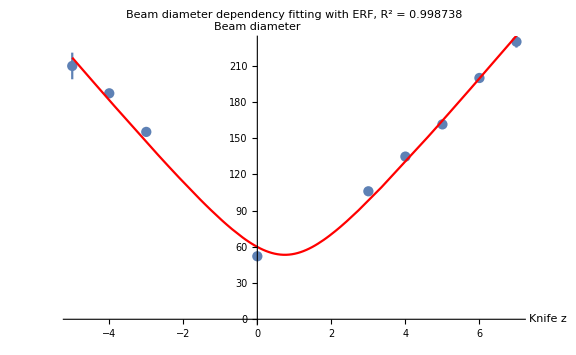

```mathematica
CalculateERF[]; (* Calculating beam diameter with Gauss function *)
BeamERFExport//TableForm (* Showing calculated data in a table *)
If[Experiments≥4,GetBeamPropogationFit[BeamERFPlot,"ERF"] ,"Not enough measured points for waist calculation "](* Beam parameters calculating *)
```

R | W | dW
-5. | 199.672 | 43.1369
-4. | 187.818 | 7.04779
-3. | 162.821 | 3.86635
0. | 55.5828 | 1.32279
3. | 109.023 | 1.89185
4. | 133.618 | 2.04286
5. | 154.956 | 2.17878
6. | 191.297 | 3.41977
7. | 203.361 | 15.4205

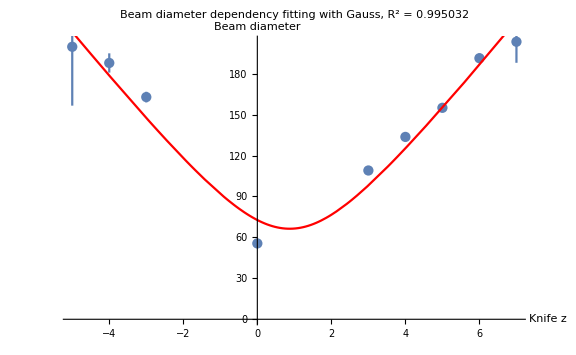

```mathematica
CalculateGauss[]; (* Calculating beam diameter with Gauss function *)
BeamGaussExport//TableForm (* Showing calculated data in a table *)
If[Experiments≥4,GetBeamPropogationFit[BeamGaussPlot,"Gauss"] ,"Not enough measured points for waist calculation "](* Beam parameters calculating *)
```

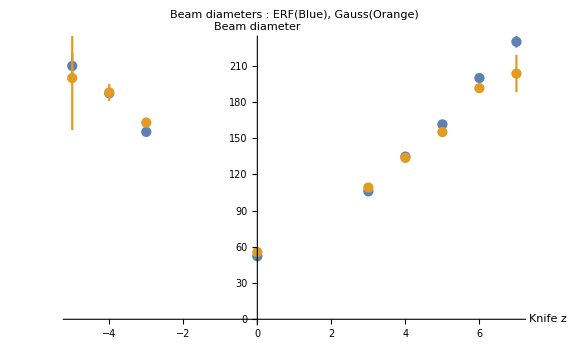

```mathematica
ERFandGaussPlot=ErrorListPlot[{BeamERFPlot,BeamGaussPlot},
PlotLabel->"Beam diameters : ERF(Blue), Gauss(Orange)",AxesLabel->{"Knife z","Beam diameter"},ImageSize->Large](* Plotting everything in one Plot *)
Export[FileNameJoin[{exportDir,"ERFandGaussBeamDiameterPlot.png"}],ERFandGaussPlot];(* Exporting previous plot *)
```

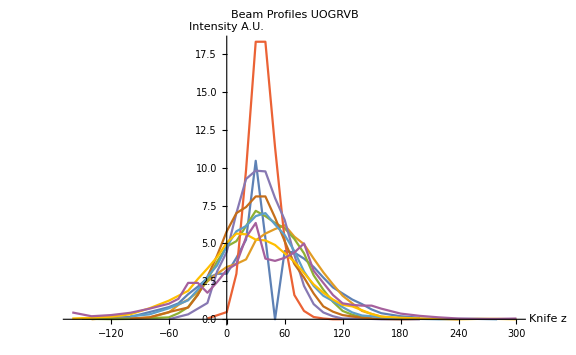

```mathematica
BeamProfiles=Table[MyDerivative[AllData[[i,3;;,1;;2]]],{i,2,Length[AllData]}];(* Calculating beam profiles *)
BeamProfilesPlot=ListPlot[BeamProfiles,Joined->True,ImageSize->Large,PlotRange->All, PlotLabel->"Beam Profiles UOGRVB",AxesLabel->{"Knife z","Intensity A.U."}](* Plotting beam profiles *)
Export[FileNameJoin[{exportDir,"BeamProfilesPlot.png"}],BeamProfilesPlot];(* Exporting previous plot *)
Export[FileNameJoin[{exportDir,"BeamProfiles.xlsx"}],BeamProfiles];(* Exporting beam profiles raw data *)
```

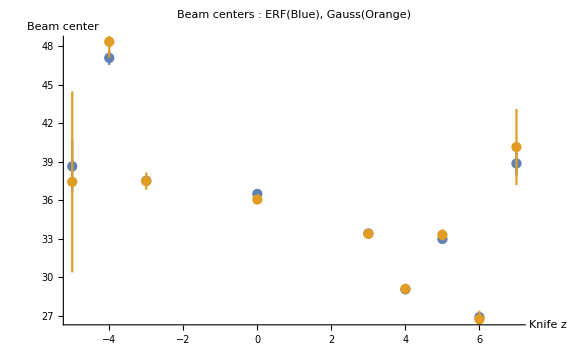

```mathematica
ERFandGaussBeamCentresPlot=ErrorListPlot[{BeamERFCenterPlot,BeamGaussCenterPlot},
PlotLabel->"Beam centers : ERF(Blue), Gauss(Orange)",AxesLabel->{"Knife z","Beam center"},PlotRange->All,ImageSize->Large](* Plotting dependency of beam centers from Knife z *)
Export[FileNameJoin[{exportDir,"Beam centers.png"}],ERFandGaussBeamCentresPlot];(* Exporting previous plot *)
```